# Predicting Climate Risks

## MGT529- Data Science and Machine Learning II

Jeanne Fernandez, Dario Scalabrin

## Data Loading & Cleaning

### Data Loading

```mathematica
ds = Import["https://raw.githubusercontent.com/scalabrindario/predicting-climate-risks/main/data/dataset.csv", "Dataset", "HeaderLines" -> 1];(*Import dataset sample*)
comp = Import["https://raw.githubusercontent.com/scalabrindario/predicting-climate-risks/main/data/company_information.csv", "Dataset", "HeaderLines" -> 1];(*Import company information*)
```

### Data Cleaning

```mathematica
ds = KeyDrop[{""}]@ds; (*Drop emtpy column*)
ds = KeyDrop[{"Activity Description"}]@ds; (*Drop activity column*)
ds = ds[All,KeyMap[Replace[{"Ultimate Parent Name"->"Company", "Ultimate Parent ISIN"->"ISIN","ExposureScore_Composite_ModerateHigh_2020" -> "Risk2020",
"ExposureScore_Composite_ModerateHigh_2030" -> "Risk2030","ExposureScore_Composite_ModerateHigh_2040" -> "Risk2040","ExposureScore_Composite_ModerateHigh_2050" -> "Risk2050","ExposureScore_Composite_ModerateHigh_2060" ->"Risk2060",
"ExposureScore_Composite_ModerateHigh_2070" -> "Risk2070","ExposureScore_Composite_ModerateHigh_2080" -> "Risk2080",
"ExposureScore_Composite_ModerateHigh_2090"-> "Risk2090"}]]];(*Rename columns name*)
RandomSample[ds, 5]
comp = KeyDrop[{""}]@comp; (*Drop emtpy column*)
RandomSample[comp, 5]
```

## Feature Engineering

### Integral Score

Our goal it to give a summary of the risk approximation by decade into one scalar statistic, called Integral Score. 
We first visualise several options for this score, given the risk values by decade.
One can fit a function given the risk approximation for several years, and then integrate the resulting curve.
The choice of score then boils down to the choice of approximation.

{68,72,70,79,85,87,89,90}

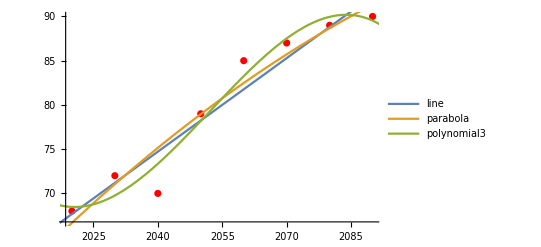

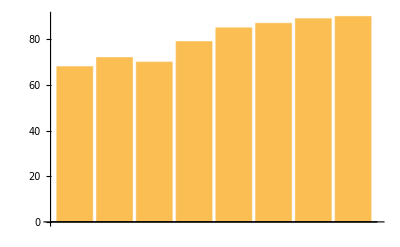

Linear approximation (line): 6540.95

Quardatic approximation (parabola): 6537.14

Third degree approximation (polynomial3): 6489.06

Rectangle approximation (barchart): 6400

```mathematica
x = {2020, 2030, 2040,2050,2060,2070, 2080, 2090};
yRandom = Normal@Values@RandomSample[ds[All, {6;;13}],1][[1,1]] (*We pick one row at random to illustrate all the possible scores*)
data = Transpose@Normal@{x,yRandom};
line = Fit[data, {1,z}, z];
parabola = Fit[data, {1,z,z^2}, z];
polynomial3 = Fit[data, {1,z,z^2,z^3}, z];
Show[ListPlot[data,PlotStyle->Red],Plot[{line, parabola, polynomial3},{z,2010,2100}, PlotLegends->"Expressions"]]
BarChart[yRandom]
Print["Linear approximation (line): ", Integrate[line,{z,2020,2100}]]
Print["Quardatic approximation (parabola): ",Integrate[parabola,{z,2020,2100}]]
Print["Third degree approximation (polynomial3): ",Integrate[polynomial3,{z,2020,2100}]]
Print["Rectangle approximation (barchart): ",(Total@yRandom)*10]
```

We note that all the approximations are in the same order of magnitude. For the sake of simplicity and to avoid overfitting, we choose the linear approximation. We add the chosen Integral Score to the dataset.

```mathematica
intColumn =ds[All,<|"integralScore"->Integrate[
Fit[Transpose@Normal@{x,{#Risk2020,#Risk2030,#Risk2040,#Risk2050,#Risk2060,#Risk2070,#Risk2080,#Risk2090}}, {1,z}, z]
,{z,2020,2100}]|>&];
newds=Join[ds,intColumn,2];
RandomSample[newds, 5]
```

### Computing Average of Integral Score

```mathematica
avgds= newds[GroupBy[{#Company}&]/*Values,<|"Company"->Query[First,"Company"],"ISIN"->Query[First,"ISIN"],"integralScore"->Query[Mean,"integralScore"]|>] ;(*Grouped and computed operations on some columns*)
RandomSample[avgds, 5]
```

### Merge the two datasets

```mathematica
merged = JoinAcross[avgds,comp,Key["ISIN"]];(*Merged two datasets and dropped rows without ISIN value*)
RandomSample[merged,5]
```

### Create Ratings

```mathematica
MinMaxScaler[value_]:=Rescale[value,{Min[merged[All, "integralScore"]],Max[merged[All, "integralScore"]]}];
MinMaxScaledList = Map[MinMaxScaler, merged[All, "integralScore"]];
RatingCreator[value_]:= 
If[Between[value,{0,0.2}], "A", 
If[Between[value,{0.2,0.4}], "B", 
If[Between[value,{0.4,0.6}], "C",
If[Between[value,{0.6,0.8}], "D",
If[Between[value,{0.8,1}], "E",   
]]]]]; (*Convert a numerical variable into a category*)
RatingsList = Map[RatingCreator, MinMaxScaledList];
IntScaledDat=Dataset[<|"IntScaled"->#|>&/@Normal[MinMaxScaledList]]; (*Convert the list into a dataset*)
RatingsDat=Dataset[<|"Ratings"->#|>&/@Normal[RatingsList]];(*Convert the list into a dataset*)
finalds = Join[merged,IntScaledDat,2]; (*Add Scaled Integral column to the dataset*)
finalds = Join[finalds,RatingsDat,2];(*Add Rating column to the dataset*)
RandomSample[finalds, 5]
```

### Add to the dataset the Total Carbon Intensity

```mathematica
CI1L = Normal[finalds[All, "Carbon Intensity-Scope 1 (tonnes CO2e/USD mn)"]];
CI2L = Normal[finalds[All,  "Carbon Intensity-Scope 2 (tonnes CO2e/USD mn)"]];
CI3L = Normal[finalds[All,  "Carbon Intensity-Scope 3 (tonnes CO2e/USD mn)"]];
CItotDat=Dataset[<|"Carbon Intensity Total (tonnes CO2e/USD mn)"->#|>&/@Normal[Total[{CI1L, CI2L, CI3L}]]]; (*Convert the list into a dataset*)
finalds = Join[finalds,CItotDat,2]; (*Add Carbon Intensity-Scope Total column to the dataset*)
RandomSample[finalds,5]
```

## Exploratory Data Analysis

```mathematica
Dimensions@finalds
```

{1768,16}

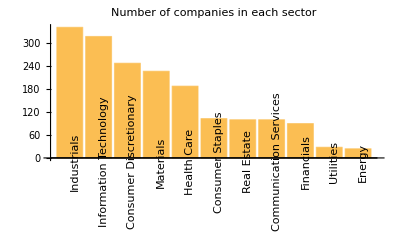

```mathematica
x1 = ReverseSort@Counts[finalds[All, "GICS Sector Name"]];
BarChart[x1,ChartLabels ->Placed[Normal@Keys@x1,Below, Rotate[#, Pi/2] &],PlotLabel->"Number of companies in each sector"]
```

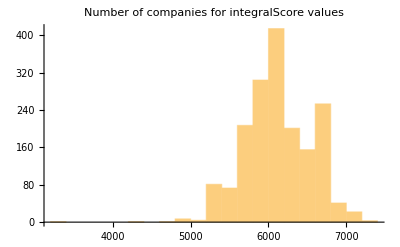

```mathematica
Histogram[finalds[All, "integralScore"],PlotLabel->"Number of companies for integralScore values"]
```

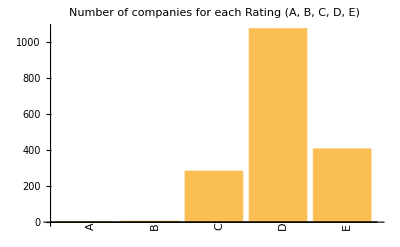

```mathematica
x2 = Counts[finalds[All, "Ratings"]];
x3 = {x2["A"], x2["B"], x2["C"], x2["D"], x2["E"]};
BarChart[x3,ChartLabels ->Placed[{"A","B","C","D","E"},Below, Rotate[#, Pi/2] &],PlotLabel->"Number of companies for each Rating (A, B, C, D, E) "]
```

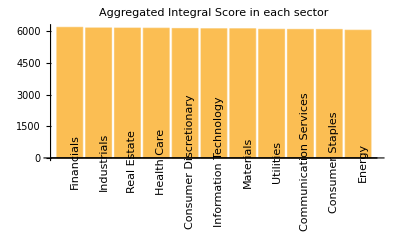

```mathematica
x4 = ReverseSort@finalds[GroupBy["GICS Sector Name"],Mean,{"integralScore"}];
x5 = Flatten@Values@Values@Normal@x4;
BarChart[x5,ChartLabels -> Placed[Normal@Keys@x4,Below, Rotate[#, Pi/2] &],PlotLabel->"Aggregated Integral Score in each sector"]
```

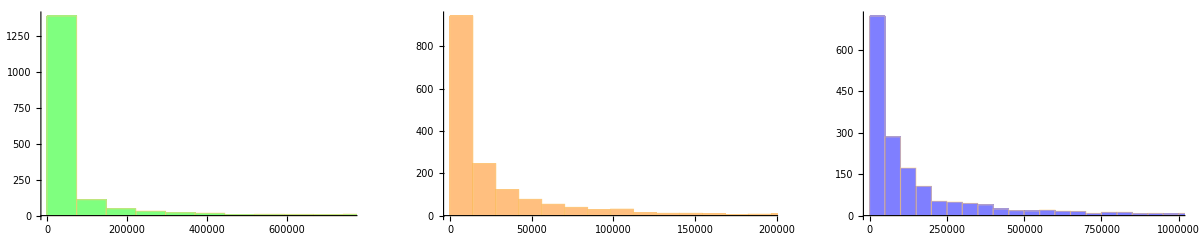

```mathematica
g1=Histogram[finalds[All, "Carbon-Scope 1  (tonnes CO2e)"],ChartStyle->{Directive[Green,Opacity[.5]]}];
g2=Histogram[finalds[All, "Carbon-Scope 2  (tonnes CO2e)"],ChartStyle->{Directive[Orange,Opacity[.5]]}];
g3=Histogram[finalds[All, "Carbon-Scope 3 (tonnes CO2e)"],ChartStyle->{Directive[Blue,Opacity[.5]]}];
GraphicsRow[{g1,g2, g3},PlotLabel->"Carbon-Scope 1,2,3 (tonnes CO2e)"]
```

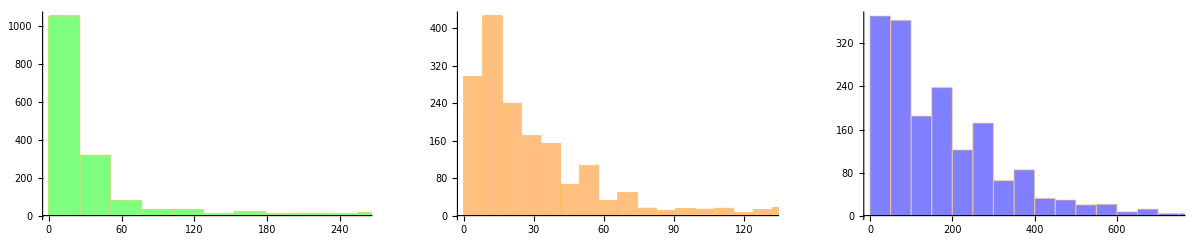

```mathematica
j1=Histogram[finalds[All, "Carbon Intensity-Scope 1 (tonnes CO2e/USD mn)"],ChartStyle->{Directive[Green,Opacity[.5]]}];
j2=Histogram[finalds[All, "Carbon Intensity-Scope 2 (tonnes CO2e/USD mn)"],ChartStyle->{Directive[Orange,Opacity[.5]]}];
j3=Histogram[finalds[All, "Carbon Intensity-Scope 3 (tonnes CO2e/USD mn)"],ChartStyle->{Directive[Blue,Opacity[.5]]}];
GraphicsRow[{j1,j2, j3},PlotLabel->"Carbon Intensity-Scope 1,2,3 (tonnes CO2e/USD mn)"]
```

```mathematica
Normal@Keys@First@finalds
```

```mathematica
{"Company","ISIN","integralScore","TCUID","GICS Sector Name","Carbon-Scope 1  (tonnes CO2e)","Carbon-Scope 2  (tonnes CO2e)","Carbon-Scope 3 (tonnes CO2e)","Carbon Intensity-Scope 1 (tonnes CO2e/USD mn)","Carbon Intensity-Scope 2 (tonnes CO2e/USD mn)","Carbon Intensity-Scope 3 (tonnes CO2e/USD mn)","Carbon Disclosure","Revenue (USD mn)","IntScaled","Ratings","Carbon Intensity Total (tonnes CO2e/USD mn)"}
```

{Company,ISIN,integralScore,TCUID,GICS Sector Name,Carbon-Scope 1  (tonnes CO2e),Carbon-Scope 2  (tonnes CO2e),Carbon-Scope 3 (tonnes CO2e),Carbon Intensity-Scope 1 (tonnes CO2e/USD mn),Carbon Intensity-Scope 2 (tonnes CO2e/USD mn),Carbon Intensity-Scope 3 (tonnes CO2e/USD mn),Carbon Disclosure,Revenue (USD mn),IntScaled,Ratings,Carbon Intensity Total (tonnes CO2e/USD mn)}

```mathematica
revLog = Normal@finalds[All,"Revenue (USD mn)" ][Log];
scope1Log =  Normal@finalds[All,"Carbon-Scope 1  (tonnes CO2e)" ][Log];
scope2Log =  Normal@finalds[All,"Carbon-Scope 2  (tonnes CO2e)" ][Log];
scope3Log =  Normal@finalds[All,"Carbon-Scope 3 (tonnes CO2e)" ][Log];
scopeTotLog =  Normal@finalds[All,"Carbon Intensity Total (tonnes CO2e/USD mn)"][Log];
```

```mathematica
dataRev  =Dataset[<|"Log of Revenues (USD mn)"->Normal@revLog |>]//Transpose;
dataScope1Log  =Dataset[<|"Log of Scope 1 emissons (tonnes CO2e)"->Normal@scope1Log |>]//Transpose;
dataScope2Log  =Dataset[<|"Log of Scope 2 emissons (tonnes CO2e)"->Normal@scope2Log |>]//Transpose;
dataScope3Log  =Dataset[<|"Log of Scope 3 emissons (tonnes CO2e)"->Normal@scope3Log |>]//Transpose;
dataScopeTotLog  =Dataset[<|"Log of Carbon Intensity Total (tonnes CO2e/USD mn)"->Normal@scopeTotLog |>]//Transpose;
finalds2 = Join[finalds,dataRev ,2];
finalds3 = Join[finalds2,dataScope1Log ,2];
finalds4 = Join[finalds3,dataScope2Log ,2];
finalds5 = Join[finalds4,dataScope3Log ,2];
finalds6 = Join[finalds5,dataScopeTotLog ,2];
```

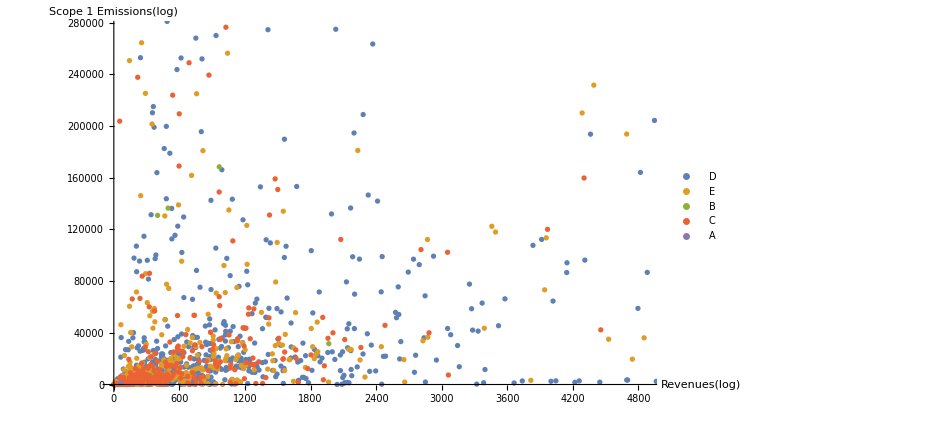

```mathematica
ListPlot[finalds3[GroupBy[Key["Ratings"]],All,{"Revenue (USD mn)","Carbon-Scope 1  (tonnes CO2e)"}], AxesLabel->{"Revenues(log)","Scope 1 Emissions(log)"}]
```

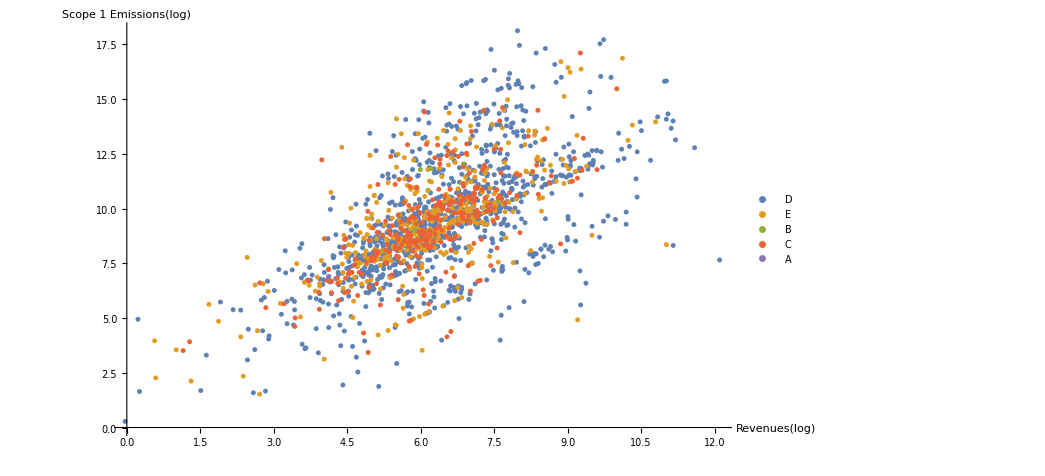

```mathematica
ListPlot[finalds3[GroupBy[Key["Ratings"]],All,{"Log of Revenues (USD mn)","Log of Scope 1 emissons (tonnes CO2e)"}], AxesLabel->{"Revenues(log)","Scope 1 Emissions(log)"}]
```

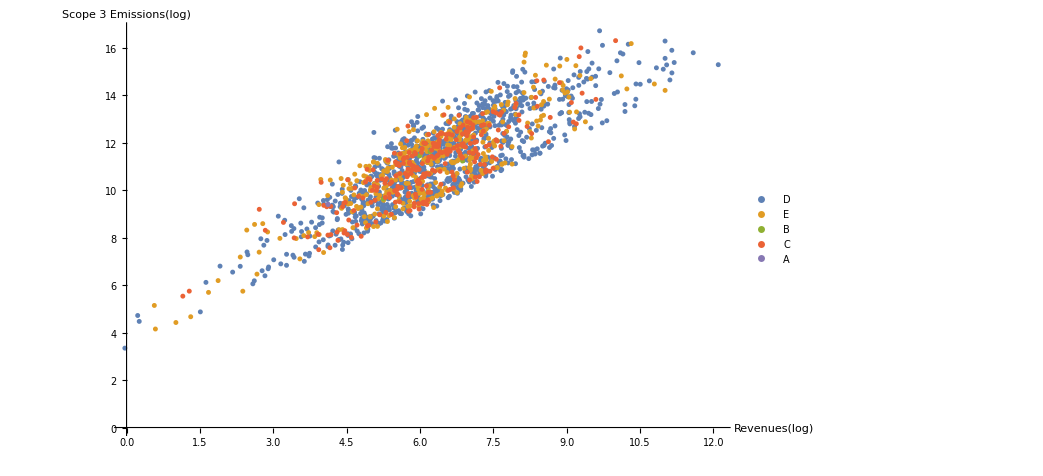

```mathematica
ListPlot[finalds5[GroupBy[Key["Ratings"]],All,{"Log of Revenues (USD mn)","Log of Scope 3 emissons (tonnes CO2e)"}], AxesLabel->{"Revenues(log)","Scope 3 Emissions(log)"}]
```

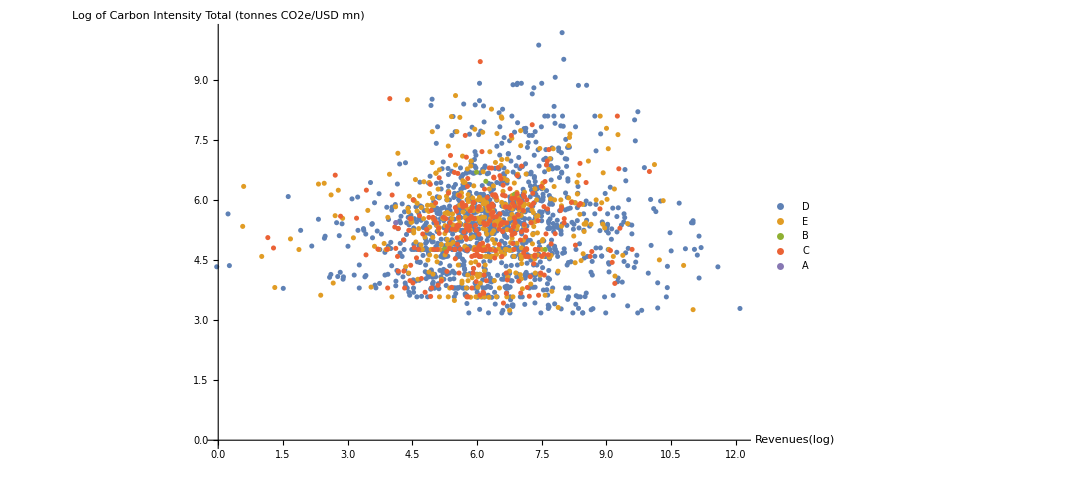

```mathematica
ListPlot[finalds6[GroupBy[Key["Ratings"]],All,{"Log of Revenues (USD mn)","Log of Carbon Intensity Total (tonnes CO2e/USD mn)"}], AxesLabel->{"Revenues(log)","Log of Carbon Intensity Total (tonnes CO2e/USD mn)"}]
```

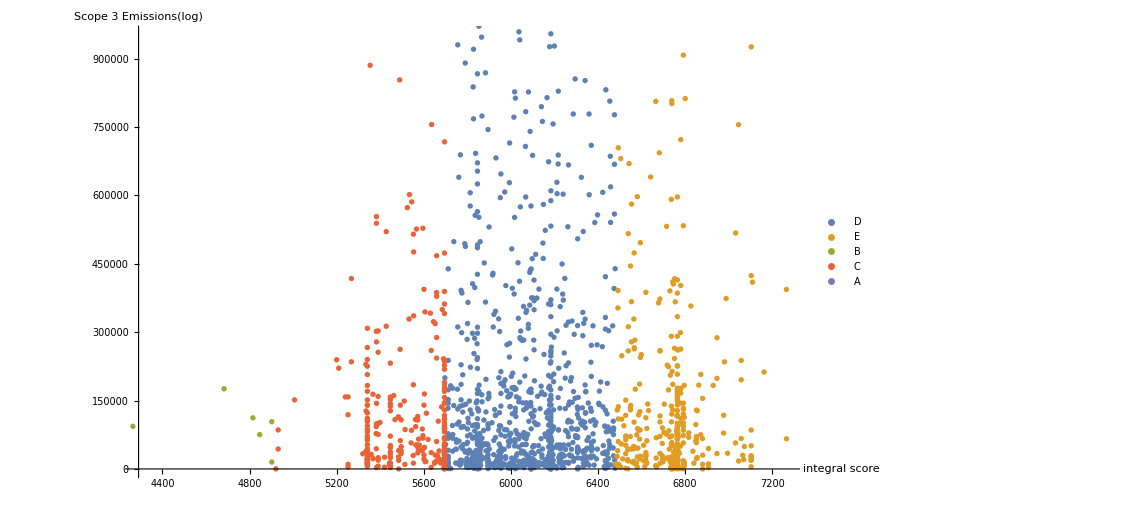

```mathematica
ListPlot[finalds5[GroupBy[Key["Ratings"]],All,{ "integralScore", "Carbon-Scope 3 (tonnes CO2e)"}], AxesLabel->{"integral score","Scope 3 Emissions(log)"}]
```

### Clustering

```mathematica
ListPlot[FindClusters[Transpose@Normal@{rev,disclosure}], PlotLabel->"Clusters"]
```

-Graphics-

```mathematica
ListPlot[FindClusters[Transpose@Normal@{finalds5[All, "Log of Scope 3 emissons (tonnes CO2e)"], finalds5[All, "elevation"]}, nClusters], PlotLabel->"Clusters"]
```

Transpose::nmtx: The first two levels of {{12.8356,13.556,15.2888,11.3399,13.3168,14.6809,12.9859,16.2847,14.6458,13.4692,«84»},Failure[Dataset,{MessageTemplate:>Dataset::partmismatch,MessageParameters→«1»}]} cannot be transposed.

FindClusters::numclus: The number of clusters nClusters can only be either a positive integer or Automatic.

Transpose::nmtx: The first two levels of {{12.8356,13.556,15.2888,11.3399,13.3168,14.6809,12.9859,16.2847,14.6458,13.4692,«84»},Failure[Dataset,{MessageTemplate:>Dataset::partmismatch,MessageParameters→«1»}]} cannot be transposed.

FindClusters::numclus: The number of clusters nClusters can only be either a positive integer or Automatic.

Transpose::nmtx: The first two levels of {{12.8356,13.556,15.2888,11.3399,13.3168,14.6809,12.9859,16.2847,14.6458,13.4692,«84»},Failure[Dataset,{MessageTemplate:>Dataset::partmismatch,MessageParameters→«1»}]} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

FindClusters::numclus: The number of clusters nClusters can only be either a positive integer or Automatic.

General::stop: Further output of FindClusters::numclus will be suppressed during this calculation.

ListPlot::lpn: FindClusters[Transpose[{{12.8356,13.556,15.2888,11.3399,13.3168,14.6809,12.9859,16.2847,14.6458,13.4692,«84»},Failure[Dataset,{MessageTemplate:>Dataset::partmismatch,MessageParameters→«1»}]}],nClusters] is not a list of numbers or pairs of numbers.

ListPlot[FindClusters[Transpose[{{12.8356,13.556,15.2888,11.3399,13.3168,14.6809,12.9859,16.2847,14.6458,13.4692,14.2034,10.9681,12.6826,15.1145,12.6195,13.6099,14.1699,14.1446,11.3311,14.6058,12.9277,14.0754,11.7997,12.0938,14.4187,15.1068,16.7172,11.6905,10.3385,11.5605,13.5438,11.1167,13.6591,13.8327,9.60396,15.8957,10.4101,6.69009,14.5861,11.4894,10.0353,10.367,9.37552,10.5962,11.5587,11.526,10.9856,15.1566,9.19479,13.6746,11.9697,10.704,12.0064,10.9702,11.8833,12.6336,10.7385,13.4798,13.5714,10.1382,13.886,10.2505,9.8139,9.3171,10.9257,11.0463,10.0015,8.16718,10.5822,9.56006,10.8659,11.2567,9.00971,9.74383,13.0979,11.979,10.8247,8.78372,13.3068,9.83084,10.5899,9.87293,9.21516,11.8897,13.5853,9.56181,12.8221,10.9142,8.86131,10.0567,9.68355,10.1564,9.50963,9.34322},Failure[Dataset,{MessageTemplate:>Dataset::partmismatch,MessageParameters→<|Type→TypeSystem`Struct[{Company,ISIN,integralScore,TCUID,GICS Sector Name,Carbon-Scope 1  (tonnes CO2e),Carbon-Scope 2  (tonnes CO2e),Carbon-Scope 3 (tonnes CO2e),Carbon Intensity-Scope 1 (tonnes CO2e/USD mn),Carbon Intensity-Scope 2 (tonnes CO2e/USD mn),Carbon Intensity-Scope 3 (tonnes CO2e/USD mn),Carbon Disclosure,Revenue (USD mn),IntScaled,Ratings,Carbon Intensity Total (tonnes CO2e/USD mn),Log of Revenues (USD mn),Log of Scope 1 emissons (tonnes CO2e),Log of Scope 2 emissons (tonnes CO2e),Log of Scope 3 emissons (tonnes CO2e)},{TypeSystem`Atom[String],TypeSystem`Atom[String],TypeSystem`Atom[Real],TypeSystem`Atom[Integer],TypeSystem`Atom[String],TypeSystem`Atom[Real],TypeSystem`Atom[Real],TypeSystem`Atom[Real],TypeSystem`Atom[Real],TypeSystem`Atom[Real],TypeSystem`Atom[Real],TypeSystem`Atom[String],TypeSystem`Atom[Real],TypeSystem`Atom[Real],TypeSystem`Atom[TypeSystem`Enumeration[A,B,C,D,E]],TypeSystem`Atom[Real],TypeSystem`Atom[Real],TypeSystem`Atom[Real],TypeSystem`Atom[Real],TypeSystem`Atom[Real]}],Part→elevation,Symbol→Part|>}]}],nClusters],PlotLabel→Clusters]

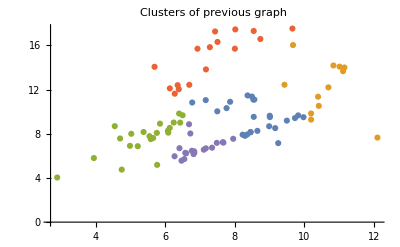

```mathematica
nClusters = 5;
ListPlot[FindClusters[Transpose@Normal@{rev,disclosure}, nClusters], PlotLabel->"Clusters"]
```

## Machine Learning

### Dataset Preparation

Prepare the dataset to use as an input for the machine learning models that we are going to create. In particular, we are going to divide the dataset in two new dataset: Training set, which includes 80% of all the rows of the dataset, while the Test set, which includes the remaining 20%.
The training set will be used to train our models, while the test set in order to understand the accuracy of our models.

```mathematica
datasetML = KeyDrop[{"Company", "ISIN", "TCUID", "integralScore", "IntScaled","Carbon-Scope 1  (tonnes CO2e)", "Carbon-Scope 2  (tonnes CO2e)", "Carbon-Scope 3 (tonnes CO2e)", "Carbon Intensity Total (tonnes CO2e/USD mn)"}]@finalds; (*Drop columns that are not needed for machine learning techniques*)
{nobs,ncol}=Dimensions[datasetML];(*Retrieve the number of rows and columns of the dataset*)
{trainingset,testset}=TakeDrop[RandomSample[datasetML],Round[nobs*0.8,1]];(*Divide the dataset in training set and test set*)
AccuracyAss = Association[];(*Create an empty association, to fill in with accuracy of our models*)
```

### Classification

#### Logistic Regression

Train a classifier using probabilities from linear combinations of features

```mathematica
cRisk = Classify[trainingset->"Ratings",Method->"LogisticRegression"]
Information[cRisk]
```

ClassifierFunction[…]

Classifier information
Data type | Mixed (number: 6)
Classes | ,,BCDE
Accuracy | (60.4.) %
Method | LogisticRegression
Single evaluation time | 1.82 ms/example
Batch evaluation speed | 51.5 examples/ms
Loss | 0.993 ± 0.054
Model memory | 361. kB
Training examples used | 1414 examples
Training time | 1.58 s
 |

The accuracy is: 0.615819

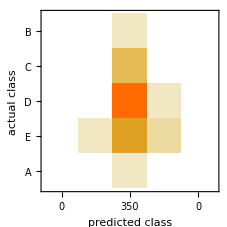

```mathematica
cm =ClassifierMeasurements[cRisk,testset]; (*Test our classifier on the test set*)
Print["The accuracy is: ",cm["Accuracy"] ](*Plot the accuracy of our model*)
AccuracyAss = Append[AccuracyAss, "LogisticRegression"->cm["Accuracy"]];
cm["ConfusionMatrixPlot"] (*Plot the Confusion Matrix*)
```

#### Gradient Boosted Trees

Train a classifier using an ensemble of trees trained with gradient boosting

```mathematica
cRisk = Classify[trainingset->"Ratings",Method->"GradientBoostedTrees"]
Information[cRisk]
```

ClassifierFunction[…]

Classifier information
Data type | Mixed (number: 6)
Classes | ,,BCDE
Accuracy | (60.52.0) %
Method | GradientBoostedTrees
Single evaluation time | 9.37 ms/example
Batch evaluation speed | 6.06 examples/ms
Loss | 0.982 ± 0.026
Model memory | 763. kB
Training examples used | 1414 examples
Training time | 2.14 s
 |

The accuracy is: 0.612994

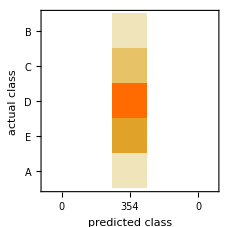

```mathematica
cm =ClassifierMeasurements[cRisk,testset]; (*Test our classifier on the test set*)
Print["The accuracy is: ",cm["Accuracy"] ](*Plot the accuracy of our model*)
AccuracyAss = Append[AccuracyAss, "GradientBoostedTrees"->cm["Accuracy"]];
cm["ConfusionMatrixPlot"] (*Plot the Confusion Matrix*)
```

#### RandomForest

Train a classifier using Breiman–Cutler ensembles of decision trees

```mathematica
cRisk = Classify[trainingset->"Ratings",Method->"RandomForest"]
Information[cRisk]
```

ClassifierFunction[…]

Classifier information
Data type | Mixed (number: 6)
Classes | ,,BCDE
Accuracy | (61.4.) %
Method | RandomForest
Single evaluation time | 2.93 ms/example
Batch evaluation speed | 24.6 examples/ms
Loss | 1.11 ± 0.029
Model memory | 498. kB
Training examples used | 1414 examples
Training time | 2.43 s
 |

```mathematica
cm =ClassifierMeasurements[cRisk,testset]; (*Test our classifier on the test set*)
Print["The accuracy is: ",cm["Accuracy"] ](*Plot the accuracy of our model*)
AccuracyAss = Append[AccuracyAss, "RandomForest"->cm["Accuracy"]];
cm["ConfusionMatrixPlot"] (*Plot the Confusion Matrix*)
```

The accuracy is: 0.612994

-Graphics-

#### SupportVectorMachine

Train a classifier using a support vector machine

```mathematica
cRisk = Classify[trainingset->"Ratings",Method->"SupportVectorMachine"]
Information[cRisk]
```

ClassifierFunction[…]

Classifier information
Data type | Mixed (number: 6)
Classes | ,,BCDE
Accuracy | (60.62.0) %
Method | SupportVectorMachine
Single evaluation time | 3.95 ms/example
Batch evaluation speed | 14.1 examples/ms
Loss | 1.14 ± 0.048
Model memory | 1.27 MB
Training examples used | 1414 examples
Training time | 3.31 s
 |

```mathematica
cm =ClassifierMeasurements[cRisk,testset]; (*Test our classifier on the test set*)
Print["The accuracy is: ",cm["Accuracy"] ](*Plot the accuracy of our model*)
AccuracyAss = Append[AccuracyAss, "SupportVectorMachine"->cm["Accuracy"]];
cm["ConfusionMatrixPlot"] (*Plot the Confusion Matrix*)
```

The accuracy is: 0.612994

-Graphics-

#### Nearest Neighbors

Train a classifier from nearest neighbor examples

```mathematica
cRisk = Classify[trainingset->"Ratings",Method->"NearestNeighbors"]
Information[cRisk]
```

ClassifierFunction[…]

Classifier information
Data type | Mixed (number: 6)
Classes | ,,BCDE
Accuracy | (61.4.) %
Method | NearestNeighbors
Single evaluation time | 1.99 ms/example
Batch evaluation speed | 30.6 examples/ms
Loss | 0.983 ± 0.047
Model memory | 755. kB
Training examples used | 1414 examples
Training time | 332. ms
 |

```mathematica
cm =ClassifierMeasurements[cRisk,testset]; (*Test our classifier on the test set*)
Print["The accuracy is: ",cm["Accuracy"] ](*Plot the accuracy of our model*)
AccuracyAss = Append[AccuracyAss, "NearestNeighbors"->cm["Accuracy"]];
cm["ConfusionMatrixPlot"] (*Plot the Confusion Matrix*)
```

The accuracy is: 0.612994

-Graphics-

### Neural Network

#### Encoding Data

Categorical variables cannot be used directly in neural networks and must be encoded as arrays.
Therefore, we create “Class” encoders that encode the categorical variables as one-hot encoded vectors

```mathematica
sectorEncoder=NetEncoder[{"Class",DeleteDuplicates[Normal[datasetML[All,"GICS Sector Name"]]],"UnitVector"}]
disclosureEncoder=NetEncoder[{"Class",DeleteDuplicates[Normal[datasetML[All, "Carbon Disclosure"]]],"UnitVector"}]
```

NetEncoder[<>]

NetEncoder[<>]

Applying the encoders to class labels produces unit vectors

```mathematica
sectorEncoder/@DeleteDuplicates[Normal[trainingset[All,"GICS Sector Name"]]];
disclosureEncoder/@DeleteDuplicates[Normal[trainingset[All,"Carbon Disclosure"]]];
```

Applying the Decoder to class labels that we want to predict

```mathematica
ratingsDecoder = NetDecoder[{"Class",DeleteDuplicates[Normal[datasetML[All, "Ratings"]]] }];
```

#### Create a Network

Create a network with an input corresponding to each feature and using a “Categorize” decoder to interpret the output of the net
The input features are first concatenated together before being further processed.

```mathematica
net=NetGraph[{CatenateLayer[],LinearLayer[],LogisticSigmoid},
{{NetPort["GICS Sector Name"],NetPort["Carbon Intensity-Scope 1 (tonnes CO2e/USD mn)"],NetPort["Carbon Intensity-Scope 2 (tonnes CO2e/USD mn)"],NetPort["Carbon Intensity-Scope 3 (tonnes CO2e/USD mn)"],NetPort["Carbon Disclosure"],NetPort["Revenue (USD mn)"]}->1,1->2->3->NetPort["Ratings"]},
"GICS Sector Name"->sectorEncoder,"Carbon Intensity-Scope 1 (tonnes CO2e/USD mn)"->"Scalar","Carbon Intensity-Scope 2 (tonnes CO2e/USD mn)"->"Scalar","Carbon Intensity-Scope 3 (tonnes CO2e/USD mn)"->"Scalar","Carbon Disclosure"->disclosureEncoder,"Revenue (USD mn)"->"Scalar","Ratings"->ratingsDecoder]
```

NetGraph[<>]

#### Training the Net

Train the net on the training data. NetTrain will automatically attach a Cross Entropy Loss layer to the output of the net
We set up two parameters:
- “Max Training Rounds”: is an option that specifies how many times to traverse the training data
- “Learning Rate”: is an option that specifies the rate at which to adjust neural net weights in order to minimize the training loss.

```mathematica
results=NetTrain[net,trainingset,All,MaxTrainingRounds->1000, LearningRate->0.01];
netTrained=results["TrainedNet"]
```

NetGraph[<>]

#### Testing the Trained Neural Network

Plot the accuracy of the Neural Network on the Test Set

```mathematica
Print["The accuracy is: ",NetMeasurements[netTrained,testset,"Accuracy"]]
AccuracyAss = Append[AccuracyAss, "NeuralNetwork"->NetMeasurements[netTrained,testset,"Accuracy"]];
```

The accuracy is: 0.80113

### Comparing Accuracies

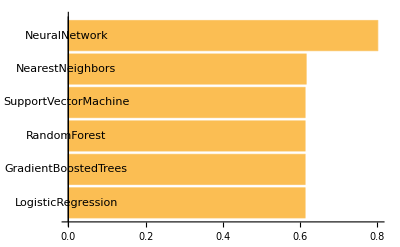

```mathematica
BarChart[Sort[AccuracyAss], ChartLabels->Keys[AccuracyAss], BarOrigin->Left]
```

### Experiment

```mathematica
probaTestRes = Mean[(probaTest[[5]]-probaTest[[#]])^2& /@Range[4]];
```

```mathematica
probaTestset = netTrained[Normal@testset[[#, 1;;6]], "Probabilities"]&/@Range[Length[testset]]
```

{<|C→0.0907458,E→0.,B→0.0447827,D→0.,A→0.|>,<|C→0.00326588,E→0.,B→0.999928,D→0.,A→0.|>,<|C→2.40358×10^-7,E→1.17147×10^-16,B→0.957007,D→6.92803×10^-8,A→6.46258×10^-21|>,<|C→1.,E→0.,B→7.0828×10^-28,D→0.,A→0.|>,<|C→0.904575,E→0.,B→6.36495×10^-6,D→0.,A→0.|>,<|C→0.999999,E→0.,B→1.35238×10^-11,D→0.,A→0.|>,<|C→1.,E→0.,B→1.69137×10^-20,D→0.,A→0.|>,<|C→0.151172,E→0.,B→0.,D→0.,A→0.|>,<|C→0.,E→0.,B→0.,D→0.,A→0.|>,<|C→0.998924,E→0.,B→1.6076×10^-7,D→0.,A→0.|>,<|C→0.557896,E→0.,B→0.0000970325,D→0.,A→0.|>,<|C→0.693325,E→2.4995×10^-15,B→0.824478,D→6.37329×10^-11,A→1.31429×10^-22|>,<|C→0.00215289,E→4.5963×10^-27,B→0.0000475067,D→1.2683×10^-17,A→0.|>,<|C→0.0000312321,E→2.24746×10^-18,B→5.24151×10^-35,D→2.15379×10^-30,A→0.|>,<|C→0.,E→0.,B→0.,D→0.,A→0.|>,<|C→1.25841×10^-7,E→1.9732×10^-13,B→0.913575,D→0.000110415,A→6.60717×10^-33|>,<|C→0.,E→3.49665×10^-19,B→0.,D→0.,A→0.|>,<|C→0.000599024,E→2.19356×10^-7,B→0.614213,D→0.0011589,A→4.19246×10^-16|>,<|C→0.985779,E→0.,B→0.0000286262,D→4.28784×10^-38,A→0.|>}

```mathematica
probaTestset = Sort[probaTestset[[#]]]&/@Range[Length[probaTestset]]
```

{<|E→0.,B→0.,D→0.,A→1.41743×10^-23,C→1.29913×10^-8|>,<|C→8.6044×10^-11,B→0.0000636843,E→0.000271905,A→0.298534,D→0.969511|>,<|E→0.,B→0.,D→0.,A→0.,C→1.|>,<|D→1.39183×10^-19,E→9.70801×10^-18,B→7.74103×10^-13,C→5.38966×10^-8,A→0.00502255|>,<|B→0.,D→5.41664×10^-30,E→2.32077×10^-22,A→0.000581846,C→1.|>,<|B→1.03112×10^-13,D→5.42167×10^-12,E→5.46488×10^-10,C→9.10605×10^-6,A→0.0012528|>,<|E→0.,B→0.,D→0.,C→1.01553×10^-11,A→6.58128×10^-8|>,<|E→0.,B→0.,D→0.,A→1.5991×10^-13,C→7.5776×10^-10|>,<|D→9.56097×10^-17,E→9.28918×10^-16,B→1.72985×10^-10,C→2.40104×10^-8,A→0.00808517|>,<|E→1.69969×10^-11,B→1.30404×10^-10,C→1.4364×10^-10,D→3.17033×10^-7,A→0.101681|>,<|E→0.,B→0.,D→0.,A→0.,C→1.|>,<|E→0.,B→0.,D→0.,A→0.,C→1.04879×10^-16|>,<|B→1.72387×10^-11,E→5.41627×10^-11,C→5.61055×10^-10,D→3.17989×10^-7,A→0.113507|>,<|E→0.,B→0.,D→0.,A→1.01165×10^-26,C→7.72471×10^-14|>,<|B→0.,E→1.38583×10^-33,D→3.79977×10^-31,A→0.0267534,C→0.993888|>,<|E→4.622×10^-26,D→5.14481×10^-23,C→2.31063×10^-15,A→0.000267134,B→0.563507|>,<|C→2.24735×10^-30,D→2.79903×10^-28,E→2.72048×10^-22,A→3.33943×10^-9,B→0.795784|>,<|D→4.7002×10^-19,E→3.0881×10^-17,B→1.43039×10^-12,C→6.24319×10^-8,A→0.00563324|>,<|D→0.,E→6.92946×10^-34,B→2.63364×10^-21,A→2.37099×10^-6,C→0.0000176597|>}

```mathematica
test = <|"E"->0.2,"B"->0.2,"D"->0.2,"A"->0.2,"C"->0.2|>
```

<|E→0.2,B→0.2,D→0.2,A→0.2,C→0.2|>

```mathematica
Mean[(test[[5]]-test[[#]])^2& /@Range[4]]
```

0.

```mathematica
Mean[(probaTestset[[1,5]]-probaTestset[[1,#]])^2& /@Range[4]]
```

1.

## Creating the API

### Defining the API

```mathematica
apiFunc = APIFunction[{
"Sector" -> "String" -> "Financials",
 "CarbInt1" -> "Number" -> 10000,
"CarbInt2" -> "Number" -> 10000,
"CarbInt3" -> "Number" -> 10000,
"CarbDisc" -> "String" -> "Value derived from data provided in Environmental/CSR",
"Revenues" -> "Number" -> 10000
},
netTrained[{#Sector, #CarbInt1, #CarbInt2,  #CarbInt3, #CarbDisc,  #Revenues}]&
];
```

### Deploying the API

```mathematica
apiFuncDeployed = CloudDeploy[
apiFunc,
"WebServices/APIRiskRating",
Permissions -> "Public"]
```

CloudObject[https://www.wolframcloud.com/obj/dario.scalabrin/WebServices/APIRiskRating]